```mathematica
Clear[MethodOfDescent];
MethodOfDescent[list_]:=Module[{l=list},
Clear[Overlap,slope,edges,edgeset,Tree];
Overlap=Partition[l,2,1];
slope[{a_,b_}]:=b-a;
edges[{a_,b_}]:={a->(b-a),b->(b-a)};
edgeset={};
Tree={list};
While[
Length[Overlap]≠0,
{
edgeset=Union[edgeset,Flatten[Map[edges,Overlap]]],
Overlap=Map[slope,Overlap],
If[Length[Overlap]==1,RootVertex=Overlap,Continue],
Overlap=Partition[Overlap,2,1]
};
];
Return[{edgeset,l,RootVertex}];
]
```

```mathematica
(*Reallocate Memory to store the data*)
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
(*Set Working Directory*)
(*Windows should be:*)
(*"C:\\Users\\<Username>\\<Where_ever_the_data_is_probably_Downloads>"*)
SetDirectory["/home/adam/Desktop/Modeling/Data"];
```

```mathematica
(*Load the data*)
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
(*To turn years to Ints*)
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData,Produced,Consumed]
(*Separate Data by state*)
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
StateData={AZData,TXData,NMData,CAData};
(*Separate By Production and Consumption*)
Consumed=Drop[Map[First,Datastuff[[2]]],2];
Produced=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
(*Functions for Working With Arrays*)
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]];
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]];
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
(*Separates Production Variables by State*)
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
(*Separates Consumption Variables by State*)
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Clear[TimeRemove]
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset,{2}]
ProducedDat=Table[TimeRemove[i],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
ConsumedDat=Table[TimeRemove[i],{i,{AZConsumed,TXConsumed,NMConsumed,CAConsumed}}];
```

```mathematica
{AZPart,TXPart,NMPart,CAPart}=Table[
Map[
DataFunc,
i,
{2}],
{i,
{AZProduced,
TXProduced,
NMProduced,
CAProduced
}
}
];

{AZPart0,TXPart0,NMPart0,CAPart0}=Table[
Map[
DataFunc,
i,
{2}],
{i,
{AZConsumed,
TXConsumed,
NMConsumed,
CAConsumed
}
}
];
```

```mathematica
Clear[RateOfChange,TableOfChange,OverlappedLists];
RateOfChange[{a_,b_}]:=b-a;
TableOfChange[data_]:=Table[RateOfChange[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];

Clear[ModelInitialization];
ModelInitialization[data_,OptionsForData_]:=Module[{d=data,o=OptionsForData},
{PSAZ,PSTX,PSNM,PSCA}=Map[OverlappedLists,d];
{PSAZ,PSTX,PSNM,PSCA}=Map[Table[TableOfChange[i],{i,#}]&,{PSAZ,PSTX,PSNM,PSCA}];
Slopes=Append[Slopes,Table[Map[o,i],{i,{PSAZ,PSTX,PSNM,PSCA}}]];
];
```

```mathematica
Clear[Model];
Model[dataset_,m_,OptionForData_]:=Module[
{data0=dataset,o=OptionForData},

Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];

ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o];

n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];

Slopes={};
Slopes=Append[Slopes,Table[Map[o,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},o];
While[
n<49,
{ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o]}
;n++];

CenterOfSeries=m;

Clear[TaylorSeries];
TaylorSeries[x_,{n0_}]:=x*(t-CenterOfSeries)^(n0-1)*(1/Factorial[n0]);

Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];
{AZSlopes,
TXSlopes,
NMSlopes,
CASlopes}=
Table[
Transpose[
PadRight[
Map[
Part[#,1]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[
Slopes,
-1]
}
]
]
]
],
{j,
{1,
2,
3,
4}
}
];

{AZMonomials,
TXMonomials,
NMMonomials,
CAMonomials}=
Table[
Table[
MapIndexed[
TaylorSeries,
i],
{i,
j}
],
{j,
{AZSlopes,
TXSlopes,
NMSlopes,
CASlopes}
}
];

{AZSystemConsumption,
TXSystemConsumption,
NMSystemConsumption,
CASystemConsumption}=
Table[
Map[Total[#]&,
i],
{i,
{AZMonomials,
TXMonomials,
NMMonomials,
CAMonomials}
}
];

Return[
{AZSystemConsumption,
TXSystemConsumption,
NMSystemConsumption,
CASystemConsumption}
];
]
```

```mathematica
(*DO NOT REMOVE*)
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},Last];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

Append::normal: Nonatomic expression expected at position 1 in Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

```mathematica
Clear[s1]
s1=Model[{AZProduced,TXProduced,NMProduced,CAProduced},49,Last];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[Slopes,{{288.359,Last[{}],Last[{}],11.6835,-6.23467,-9064.39,189.831,14967.5,0.03591,-8563.13,-6732.68},{«1»},«1»,{3933.23,«9»,-«18»}}].

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

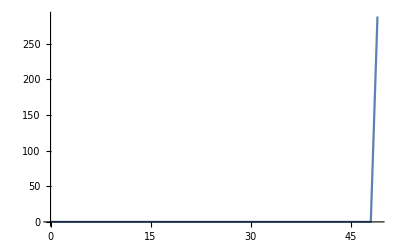

```mathematica
Show[ListLinePlot[TimeSeries[Transpose[ProducedDat[[1]][[1]]][[2]],{Transpose[ProducedDat[[1]][[1]]][[1]]}-1960]],Plot[s1[[1]][[1]],{t,0,55},PlotStyle->Orange]]
```

```mathematica
Clear[s2]
s2=Model[{AZConsumed,TXConsumed,NMConsumed,CAConsumed},49,Last];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

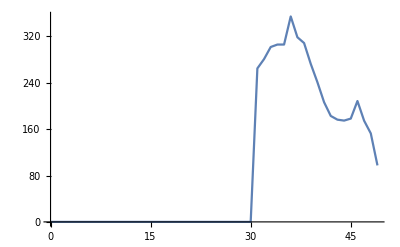

```mathematica
Show[ListLinePlot[TimeSeries[Transpose[ConsumedDat[[1]][[1]]][[2]],{Transpose[ConsumedDat[[1]][[1]]][[1]]}-1960]],Plot[s2[[1]][[1]],{t,0,55},PlotStyle->Orange]]
```

```mathematica
Clear[pathModel];
pathModel[dataset_,{indx1_,indx2_,indx3_}]:=MethodOfDescent[Transpose[dataset[[indx1]][[indx2]]][[indx3]]];
```

```mathematica
g1=pathModel[ConsumedDat,{1,1,2}];
```

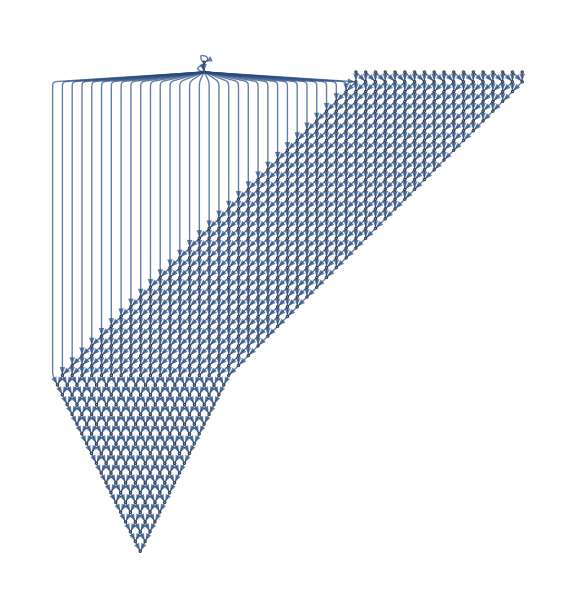

```mathematica
graph1=Graph[g1[[1]],GraphLayout->"LayeredDigraphEmbedding",ImageSize->Large]
```

```mathematica
Show[ListLinePlot[TimeSeries[Transpose[ConsumedDat[[1]][[1]]][[2]],{Transpose[ConsumedDat[[1]][[1]]][[1]]}-1960]],Plot[Total[MapIndexed[TaylorSeries,FindShortestPath[graph1,g1[[2]][[50]],g1[[3]][[1]]]]],{t,0,55},PlotStyle->Orange]]
```

-Graphics-

```mathematica
Clear[TaylorSeries0];
TaylorSeries0[x_,{n0_},m_]:=x*(t-m+1)^(n0-1)*(1/Factorial[n0]);
```

```mathematica
Clear[PathingTaylorSeries]
PathingTaylorSeries[dataset_,{indx1_,indx2_,indx3_},m_,VertexNum_]:=Show[
ListLinePlot[
TimeSeries[
Transpose[
dataset[[indx1]][[indx2]]][[indx3+1]],
{Transpose[dataset[[indx1]][[indx2]]][[indx3]]}-1960]
],
Plot[
Total[
MapIndexed[
TaylorSeries0[#1,{#2},m]&,
FindShortestPath[
graph1,
g1[[2]][[VertexNum]],
g1[[3]][[1]]
]
]
],
{t,0,55},
PlotStyle->Orange]
]
```

```mathematica
Clear[PathingTaylorSeriesLinkedbyVertexIndx]
PathingTaylorSeriesLinkedbyVertexIndx[dataset_,{indx1_,indx2_,indx3_}]:=Module[{},
g1=pathModel[dataset,{indx1,indx2,indx3+1}];
graph1=Graph[g1[[1]],GraphLayout->"LayeredDigraphEmbedding",ImageSize->Large];
MinPaths=Table[
FindShortestPath[
graph1,
g1[[2]][[i]],
g1[[3]][[1]]
],{i,1,50}
];
ShortestPaths=Table[Total[
MapIndexed[
TaylorSeries0[#1,{#2},i-1]&,
MinPaths[[i]]
]
],
{i,1,50}];
Deploy[
Manipulate[{
Show[
ListLinePlot[
TimeSeries[
Transpose[
dataset[[indx1]][[indx2]]][[indx3+1]],
{Transpose[dataset[[indx1]][[indx2]]][[indx3]]}-1960]
],
Plot[
ShortestPaths[[a]],
{t,0,55},
PlotStyle->Orange]
],HighlightGraph[graph1,PathGraph[MinPaths[[a]],DirectedEdges->True]]}
,{{a,1,"Vertex Index"},1,50,1}
]
]
]
```

```mathematica
PathingTaylorSeries[ConsumedDat,{1,1,1},43,44]
```

-Graphics-

```mathematica
PathingTaylorSeriesLinkedbyVertexIndx[ConsumedDat,{1,4,1}]
```